## Fidelidad vs pureza de Choi

```mathematica
Get["~/Documents/chaos_meets_channels/Mathematica_packages/QMB.wl"]
```

```mathematica
hx=1.;
hz=0.5;
J=1.;
L=3;
```

```mathematica
kraus=1/2*Pauli[Join[{#},ConstantArray[0,L-1]]]&/@Range[0,3];
(* Completeness relation *)
Total[#.ConjugateTranspose[#]&/@kraus]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
H=IsingNNOpenHamiltonian[hx,hz,J,L];
U[t_]:=MatrixExp[-I*H*t]
ψ=RandomChainProductState[L-1];

fidelity=purity={};
Table[
ρ=Chop[#.KroneckerProduct[IdentityMatrix[2]/2,Dyad[ψ]].ConjugateTranspose[#]&[U[t]]];
ℰρ=Total[#.ρ.ConjugateTranspose[#]&/@kraus];

(* Fidelity *)
F=Chop[Tr[MatrixPower[MatrixPower[ρ,1/2].ℰρ.MatrixPower[ρ,1/2],1/2]]^2];

(* Pureza de Choi *)
P=Chop[Purity[MatrixPartialTrace[ρ,1,{2,4}]]];

Round[F,10.^-6]==Round[P,10.^-6];
AppendTo[fidelity,{t,F}];
AppendTo[purity,{t,F}];
,{t,0,10,0.05}];
```

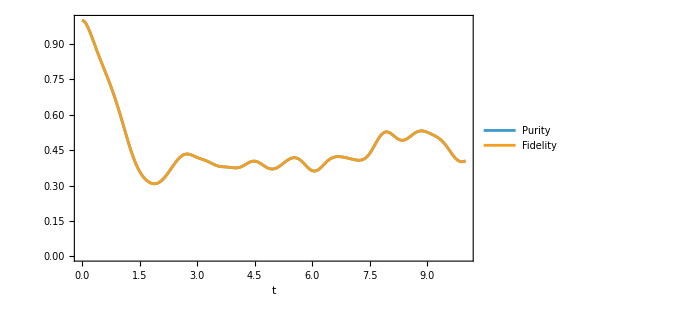

```mathematica
ListPlot[{purity,fidelity},
Joined->True,
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->22],
FrameLabel->{TraditionalForm[HoldForm[t]], Nothing},
PlotLegends->Placed[{"Purity","Fidelity"},{Right,Top}],
LabelStyle->Directive[Black,FontSize->22],
ImageSize->500
]
```

## Recycle bin

```mathematica
-1/2(PauliMatrix[0]-PauliMatrix[1])+I*1/2(PauliMatrix[0]-PauliMatrix[2])+(1-I)/2*PauliMatrix[0]//MatrixForm
```

(0 | 0
1 | 0)

```mathematica
-Outer[Times,#,#]&[{1,-1}]+I* Outer[Times,#,Conjugate[#]]&[{1,-I}]+(1-I)IdentityMatrix[2]//MatrixForm
```

(0 | 0
2 | 0)

```mathematica
(1+I)(1-I)
```

2

```mathematica
MatrixForm[ρ=Outer[Times,Conjugate[#],#]&[Normalize[{1,0,0,1}]]]
```

(1/2 | 0 | 0 | 1/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/2 | 0 | 0 | 1/2)

```mathematica
MatrixForm[ρ2=Outer[Times,Conjugate[#],#]&[Normalize[{1,0,0,0,0,0,0,1}]]]
```

(1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2)

```mathematica
kraus=1/2KroneckerProduct[PauliMatrix[#],PauliMatrix[0]]&/@{0,1,2,3};
Total[#.ConjugateTranspose[#]&/@kraus]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
kraus2=1/2KroneckerProduct[PauliMatrix[#],PauliMatrix[0],PauliMatrix[0]]&/@{0,1,2,3};
Total[#.ConjugateTranspose[#]&/@kraus2]
```

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

```mathematica
Total[#.ρ.ConjugateTranspose[#]&/@kraus]//MatrixForm
```

(1/4 | 0 | 0 | 0
0 | 1/4 | 0 | 0
0 | 0 | 1/4 | 0
0 | 0 | 0 | 1/4)

```mathematica
Total[#.ρ2.ConjugateTranspose[#]&/@kraus2]//MatrixForm
```

(1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4)

```mathematica
U=1/√2{{1,0,0,1},{0,1,1,0},{0,1,-1,0},{1,0,0,-1}}
```

{{1/(√2),0,0,1/(√2)},{0,1/(√2),1/(√2),0},{0,1/(√2),-1/(√2),0},{1/(√2),0,0,-1/(√2)}}

```mathematica
MatrixPartialTrace[U.Outer[Times,#,#]&[Flatten[KroneckerProduct[{1,0},{1,0}]]].ConjugateTranspose[U],2,2]
```

{{1/2,0},{0,1/2}}

```mathematica
MatrixPartialTrace[U.KroneckerProduct[{{1/2,0},{0,1/2}},{{1,0},{0,0}}].ConjugateTranspose[U],1,2]
```

{{1/2,0},{0,1/2}}

```mathematica
σ=U.KroneckerProduct[{{1/2,0},{0,1/2}},{{1,0},{0,0}}].ConjugateTranspose[U]
```

{{1/4,0,0,1/4},{0,1/4,-1/4,0},{0,-1/4,1/4,0},{1/4,0,0,1/4}}

```mathematica
Tr[σ.σ]
```

1/2

```mathematica
Tr[σ]
```

1

```mathematica
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"]
```

```mathematica
?MatrixPartialTrace
```

```mathematica
FullSimplify[Eigenvalues[{{a,b},{Conjugate[b],c}}]]/.{a->p ψ11,b->√(p(1-p)ψ12),c->(1-p)ψ22}
```

{1/2 (p ψ11+(1-p) ψ22-√((p ψ11-(1-p) ψ22)^2+4 √((1-p) p ψ12) Conjugate[√((1-p) p ψ12)])),1/2 (p ψ11+(1-p) ψ22+√((p ψ11-(1-p) ψ22)^2+4 √((1-p) p ψ12) Conjugate[√((1-p) p ψ12)]))}

```mathematica
Expand[Total[Sqrt[Eigenvalues[{{a,b},{Conjugate[b],c}}]]]^2]//FullSimplify
```

a+c+√(a+c-√((a-c)^2+4 b Conjugate[b])) √(a+c+√((a-c)^2+4 b Conjugate[b]))

```mathematica
(a+c-√((a-c)^2+4 b Conjugate[b]))(a+c+√((a-c)^2+4 b Conjugate[b]))//FullSimplify
```

4 a c-4 b Conjugate[b]

```mathematica
FullSimplify[Eigenvalues[{{a,b},{Conjugate[b],c}}]]
Sqrt[FullSimplify[Eigenvalues[{{a,b},{Conjugate[b],c}}]]]
Total[Sqrt[FullSimplify[Eigenvalues[{{a,b},{Conjugate[b],c}}]]]]^2//FullSimplify
```

{1/2 (a+c-√((a-c)^2+4 b Conjugate[b])),1/2 (a+c+√((a-c)^2+4 b Conjugate[b]))}

{(√(a+c-√((a-c)^2+4 b Conjugate[b])))/(√2),(√(a+c+√((a-c)^2+4 b Conjugate[b])))/(√2)}

a+c+√(a+c-√((a-c)^2+4 b Conjugate[b])) √(a+c+√((a-c)^2+4 b Conjugate[b]))

```mathematica
FullSimplify[Expand[(a+c-√((a-c)^2+4 b Conjugate[b]))(a+c+√((a-c)^2+4 b Conjugate[b]))]]
```

4 a c-4 b Conjugate[b]

```mathematica
Total[Sqrt[Eigenvalues[1/2{{ℰ00,ℰ01},{Conjugate[ℰ01],ℰ11}}]]]^2//Expand//FullSimplify
```

1/2 (ℰ00+ℰ11+√(ℰ00+ℰ11-√((ℰ00-ℰ11)^2+4 ℰ01 Conjugate[ℰ01])) √(ℰ00+ℰ11+√((ℰ00-ℰ11)^2+4 ℰ01 Conjugate[ℰ01])))

```mathematica
√((ℰ00+ℰ11-√((ℰ00-ℰ11)^2+4 ℰ01 Conjugate[ℰ01]))(ℰ00+ℰ11+√((ℰ00-ℰ11)^2+4 ℰ01 Conjugate[ℰ01])))//Expand//Simplify
```

2 √(ℰ00 ℰ11-ℰ01 Conjugate[ℰ01])

```mathematica
ρ=Chop[#.KroneckerProduct[IdentityMatrix[2]/2,Dyad[ψ]].ConjugateTranspose[#]&[U[1.2]]];
```

```mathematica
kraus=1/2{Pauli[{0,0,0}],Pauli[{1,0,0}],Pauli[{2,0,0}],Pauli[{3,0,0}]}
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

```mathematica
ℰρ=Total[#.ρ.ConjugateTranspose[#]&/@kraus];
MatrixForm[MatrixPartialTrace[ℰρ,2,{2,4}]]
```

(0.5+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.5+0. ⅈ)

```mathematica
Flatten[KroneckerProduct[{1,0},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[1.2]].Flatten[KroneckerProduct[{1,0},ψ]]//Chop

Flatten[KroneckerProduct[{1,0},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[1.2]].Flatten[KroneckerProduct[{0,1},ψ]]//Chop

Flatten[KroneckerProduct[{0,1},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[1.2]].Flatten[KroneckerProduct[{1,0},ψ]]//Chop

Flatten[KroneckerProduct[{0,1},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[1.2]].Flatten[KroneckerProduct[{0,1},ψ]]//Chop
```

0.213448

0.000937438-0.00803888 ⅈ

0.000937438+0.00803888 ⅈ

0.277477

```mathematica
Abs[Flatten[KroneckerProduct[{1,0},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[1.2]].Flatten[KroneckerProduct[{0,1},ψ]]]^2
```

0.0000655023

```mathematica
(Flatten[KroneckerProduct[{1,0},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[1.2]].Flatten[KroneckerProduct[{1,0},ψ]])*(Flatten[KroneckerProduct[{0,1},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[1.2]].Flatten[KroneckerProduct[{0,1},ψ]])//Chop
```

0.0592269

```mathematica
t=0.;
ρ=Chop[#.KroneckerProduct[IdentityMatrix[2]/2,Dyad[ψ]].ConjugateTranspose[#]&[U[t]]];
Chop@Purity[MatrixPartialTrace[ρ,1,{2,4}]]
```

1.

```mathematica
t=0.;u=U[t];

Chop[
1/2*(Flatten[KroneckerProduct[{1,0},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[t]].Flatten[KroneckerProduct[{1,0},ψ]]+Flatten[KroneckerProduct[{0,1},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[t]].Flatten[KroneckerProduct[{0,1},ψ]]+2Sqrt[(Flatten[KroneckerProduct[{1,0},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[t]].Flatten[KroneckerProduct[{1,0},ψ]])*(Flatten[KroneckerProduct[{0,1},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[t]].Flatten[KroneckerProduct[{0,1},ψ]])-Abs[Flatten[KroneckerProduct[{1,0},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[t]].Flatten[KroneckerProduct[{0,1},ψ]]]^2])]
```

0.169493-0.0303156 ⅈ